## Understanding the distribution of consumers on an implied landscape as a function of both resource availability and temperature limitations.

## Define models at equilibrium

```mathematica
(*Define Imax(T)*)Imax[T_]:=Exp[-((T-TI)^2)/β];

(*Define m(T)*)
m[T_]:=ma Exp[mb T]+mc;

(*Define f(R,T)*)
f[R_,T_]:=Imax[T] R/(R+R0);

(*Define ODEs*)
eqC:=C'[t]==(1-δ) f[R[t],T] C[t]-m[T] C[t];
eqR:=R'[t]==D  *(S-R[t])-f[R[t],T] C[t];

(*Display the system of ODEs*)
{eqC,eqR}
```

{C'[t]==-((ⅇ^(mb T) ma+mc) C[t])-(149 ⅇ^(-1/150 (-25+T)^2) C[t] R[t])/(2+R[t]),R'[t]==D (1-R[t])-(ⅇ^(-1/150 (-25+T)^2) C[t] R[t])/(2+R[t])}

## Set the equations at equilibrium from the V&V paper

```mathematica
(*Equation for Re*)
Req:=m[T] R0/((1-δ) Imax[T]-m[T]);

(*Equation for Ce*)
Ceq:=(D *((S-Req)(Req + R0)))/(Imax[T] Req);

(*Display Re and Ce*)
{Req,Ceq}
```

{(2 (ⅇ^(mb T) ma+mc))/(-149 ⅇ^(-1/150 (-25+T)^2)-ⅇ^(mb T) ma-mc),1/(2 (ⅇ^(mb T) ma+mc))D ⅇ^(1/150 (-25+T)^2) (-149 ⅇ^(-1/150 (-25+T)^2)-ⅇ^(mb T) ma-mc) (1-(2 (ⅇ^(mb T) ma+mc))/(-149 ⅇ^(-1/150 (-25+T)^2)-ⅇ^(mb T) ma-mc)) (2+(2 (ⅇ^(mb T) ma+mc))/(-149 ⅇ^(-1/150 (-25+T)^2)-ⅇ^(mb T) ma-mc))}

## Now trying to draw from a distribution for R and T to get values of C

```mathematica
(* Set parameter values *)
R0=0.5;
e=0.5;
TI=25;
δ=150;
Subscript[m, a]=0.01;
Subscript[m, b]=0.1;
Subscript[m, c]=0.05;
uppertval=40;
D=1;
S=1;
R0=2;

(*Define Imax and m as before*)
Imax[T_]:=Exp[-((T-TI)^2)/β];
m[T_]:=ma Exp[mb T]+mc;

(*Function for Ce*)
CeFunc[Req_,T_]:=(D *(S-Req)*(Req + R0))/(Imax[T] Req);
```

Set::wrsym: Symbol D is Protected.

```mathematica
(*Distributions for Req and T*)
reqDist=NormalDistribution[1.5,0.2];  (*Example:Normal distribution for Req*)
tDist=NormalDistribution[20,4]; (*Example:Uniform distribution for T*)

(*Perform a simulation with independent draws for Req and T*)
numSimulations=1000; (*Number of simulations*)

simulationResults=Table[Module[{Re,T,Ce},(*Draw values for Req and T*)Re=RandomVariate[reqDist];
T=RandomVariate[tDist];
(*Calculate Ce based on Re and T*)
Ce=CeFunc[Re,T]
{Re,T,Ce}  
(*Return the values*)
],
{numSimulations}];

(*Display the first few results*)
Take[simulationResults,10]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Take::take: Cannot take positions 1 through 10 in TerminatedEvaluation[RecursionLimit].

Take[TerminatedEvaluation[RecursionLimit],10]

## Plot these results

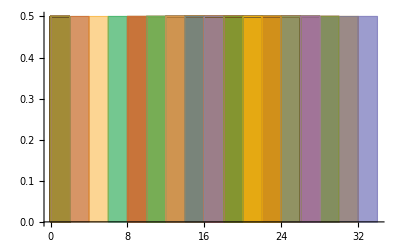

```mathematica
(*Plot histogram of Ce values*)
Histogram[simulationResults, Automatic, "Probability", 
FrameLabel->{"C Equilibrium values","Density"}]
```